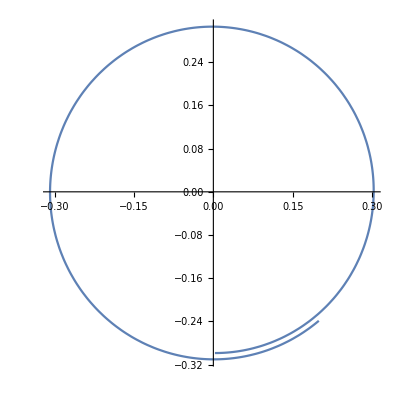

{0.316228}

1/(√10)

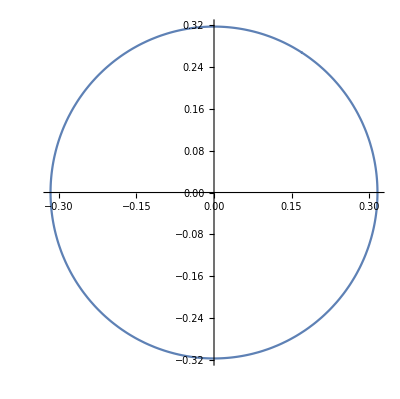

```mathematica
system={X1'[t]==X1[t]/10-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t]==X1[t]+X2[t]/10+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t],
M11'[t]==M11[t]*(-3*X1[t]^2-2*X1[t]*X2[t]-X2[t]^2+1/10)+M21[t]*(-X1[t]^2-2*X1[t]*X2[t]-3*X2[t]^2-1),
M12'[t]==M12[t]*(-3*X1[t]^2-2*X1[t]*X2[t]-X2[t]^2+1/10)+M22[t]*(-X1[t]2-2*X1[t]*X2[t]-3*X2[t]^2-1),
M21'[t]==M11[t]*(3*X1[t]^2-2*X1[t]*X2[t]+X2[t]^2+1)+M21[t]*(-X1[t] ^2+2*X1[t]*X2[t]-3*X2[t]^2+1/10),
M22'[t]==M12[t]*(3*X1[t]^2-2*X1[t]*X2[t]+X2[t]^2+1)+M22[t]*(-X1[t]^2+2*X1[t]*X2[t]-3*X2[t]^2+1/10)};
sol=NDSolve[{system,X1[0]==X2[0]==0.2,M11[0]==M22[0]==1,M12[0]==M21[0]==0},{X1,X2,M11,M12,M21,M22},{t,1000}];
ParametricPlot[Evaluate[{X1[t],X2[t]}/.sol],{t,3.62850988532908,10}]

system1={X1'[t]==X1[t]/10-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t]==X1[t]+X2[t]/10+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
tmp=Sqrt[Evaluate[X1[200]/.sol]^2+Evaluate[X2[200]/.sol]^2]
(*NDSolve[{X1[t]/.sol==tmp,X1[0]==X2[0]==0.2},{X1,X2},{t,50}]*)
Evaluate[1/Sqrt[10]]


(*FindRoot[(X1[t]^2/.sol+X2[t]^2/.sol)==tmp,{t,1,200}]*)
```